```mathematica
AlphaTest[x_]:=0≤x≤25
TextCode[text_]:=Select[
					ToCharacterCode[
						ToUpperCase[text]]-65,AlphaTest];
FromCode[textcode_]:=FromCharacterCode[textcode+65];
```

```mathematica
message=Import["http://www.repubblica.it"];
Italian=Import["http://www.corriere.it"];
English=Import["http://www.nytimes.com"];
```

```mathematica
XN=TextCode[message];
XN2=TextCode[Italian];
XN3=TextCode[English];

pita=Table[N@Count[XN2,i]/Length[XN2],{i,0,25}]
peng=Table[N@Count[XN3,i]/Length[XN3],{i,0,25}]
```

{0.11279,0.0109054,0.0457527,0.042542,0.105455,0.0114866,0.0191813,0.00863572,0.12627,0.000249107,0.00207589,0.0697777,0.0285643,0.0703313,0.0910626,0.0249384,0.00166072,0.065709,0.0477733,0.0575992,0.0249661,0.0182679,0.00138393,0.000858036,0.00157768,0.0101857}

{0.084525,0.0158778,0.0399799,0.0327291,0.0979188,0.0183619,0.0219872,0.0307486,0.0700571,0.00161128,0.00819067,0.0435717,0.0229943,0.0822759,0.0755958,0.0285666,0.00140987,0.0675059,0.0704263,0.102081,0.0221551,0.0172877,0.0176234,0.00255119,0.0229272,0.00104062}

```mathematica
?Count
```

```mathematica
Count[XN2,1]
```

394

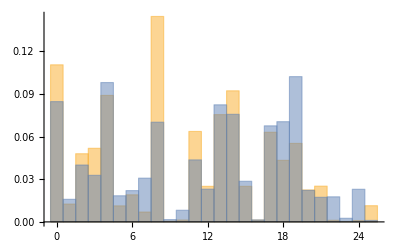

```mathematica
Histogram[{XN,XN3},26,"Probability"]
```

```mathematica
CoincidenceIndex[text_]:=
(
code=TextCode[text];


)
```

```mathematica
XN
```

{0,1,1,14,13,0,19,8,12,4,13,20,2,4,17,2,0,0,1,1,15678,3,8,19,14,17,8,0,11,4,18,15,0,15,8,21,0,8,18,18,13}
 |  |  |  |

```mathematica
Range[0,25]
```

```mathematica
f[x_]:=x+65
```

```mathematica
(#+65)&[4]
```

69

```mathematica
f[4]
```

69

```mathematica
{#,FromCharacterCode[#+65]}& 

g[x_]:={x,FromCharacterCode[x+65]}
Map[g,Range[0,25]]

TableForm@Map[{#,FromCharacterCode[#+65]}&,Range[0,25]]
```

```mathematica
MatrixForm[{{a,b},{c,d}}]
```

(a | b
c | d)

```mathematica
Tally[XN]
f(f-1)


XN
```

{{0,1735},{1,197},{14,1448},{13,1185},{19,867},{8,2269},{12,393},{4,1397},{20,353},{2,753},{17,990},{16,20},{3,813},{21,395},{6,299},{25,179},{15,393},{11,999},{18,680},{7,109},{5,177},{22,18},{24,15},{23,5},{10,21},{9,8}}

(-1+f) f

{0,1,1,14,13,0,19,8,12,4,13,20,2,4,17,2,0,0,1,1,15678,3,8,19,14,17,8,0,11,4,18,15,0,15,8,21,0,8,18,18,13}
 |  |  |  |

```mathematica
1735 1734
```

3008490

```mathematica
FullForm[{a,b,c}]
```

```mathematica
List[a,b,c]
Plus[a,b,c]
```

```mathematica
For@@{a,b,c}
```

```mathematica
FullForm[a+b+c]
```

Plus[a,b,c]

```mathematica
CoincidenceIndex[textcode_]:=N[Plus@@Map[#[[2]](#[[2]]-1)&,Tally[textcode]]/(Length[textcode](Length[textcode]-1))]
```

```mathematica
MutualIncidenceIndex[textcode_,distribution_]:=
Plus@@Table[N@Count[textcode,i]distribution[[i+1]]/Length[textcode],{i,0,25}]
```

```mathematica
X4=Table[RandomInteger[25],{4000}];
```

4000

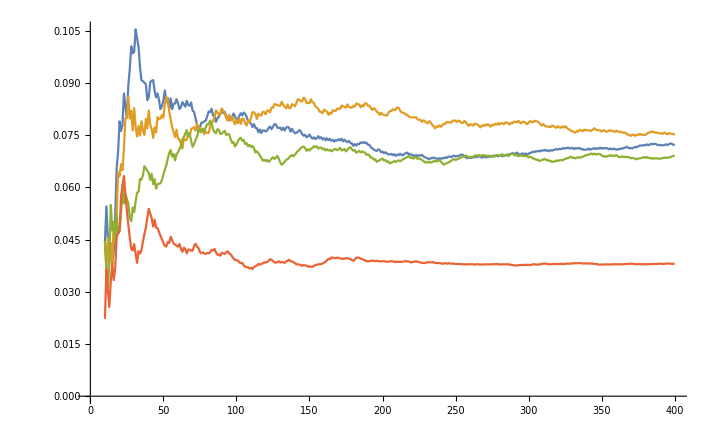

```mathematica
maxlen=Min@@Map[Length,{XN,XN2,XN3,X4}]
table=Table[{
{i,CoincidenceIndex[Take[XN,i]]},
{i,CoincidenceIndex[Take[XN2,i]]},
{i,CoincidenceIndex[Take[XN3,i]]},
{i,CoincidenceIndex[Take[X4,i]]}},{i,10,400}];
ListLinePlot[Transpose[table][[{1,2,3,4}]]]
```

```mathematica
m=26
ShiftEncode[x_,k_]:=Mod[x+k,m]
ShiftDecode[x_,k_]:=ShiftEncode[x,-k];
```

26

```mathematica
TextEncryption[encryptionfunction_,key_,text_]:=Module[{encoding},
(
	encoding[x_]:=encryptionfunction[x,key];
	Map[encoding,text]
)]

TextDecryption[encryptionfunction_,key_,text_]:=Module[{encoding},
(
	encoding[x_]:=encryptionfunction[x,key];
	Map[encoding,text]
)]
```

```mathematica
key=15
YN=TextEncryption[ShiftEncode,key,XN];
```

15

```mathematica
Manipulate[

{
Histogram[{TextEncryption[ShiftEncode,guesskey,XN2],YN},26,"Probability",ImageSize->Large],
MutualIndex[TextDecryption[ShiftDecode,guesskey,YN],pita]
},

{guesskey,0,25,1}]
```

```mathematica
Map[Hash,{483958,
525423,
504959
}]
```

{1374715000583440772,269547413338346633,8246180658051708764}